Practical 1
Solution of First order Differential Equations

```mathematica
y = .
```

```mathematica
x = .
```

```mathematica
z = .
```

Plot and solve first order Differential Equation
Ques Solve dy/dx= y

```mathematica
q1 = DSolve[{y'[x] == y[x]},y[x], x]
```

{{y[x]→ⅇ^x C[1]}}

```mathematica
q2 = y[x]/.q1/.{C[1]->1}
```

{ⅇ^x}

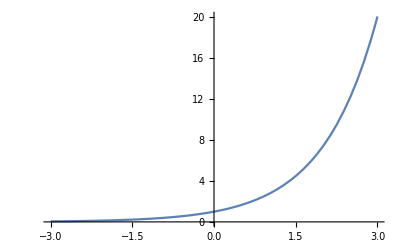

```mathematica
Plot[{q2}, {x,-3,3}]
```

Straight Integration

```mathematica
q3 = DSolve[y'[x]==x^2, y[x], x]
```

{{y[x]→x^3/3+C[1]}}

```mathematica
q4 = y[x]/.q3/.{C[1]->2}
```

{2+x^3/3}

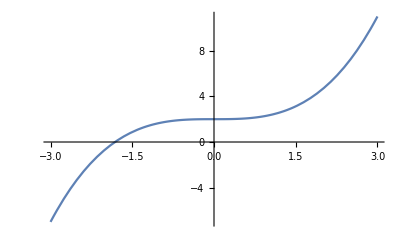

```mathematica
Plot[q4,{x,-3, 3}]
```

Another method

```mathematica
q5 = Table[y[x]/.q3/.{C[1]->k}, {k,2,5}]
```

{{2+x^3/3},{3+x^3/3},{4+x^3/3},{5+x^3/3}}

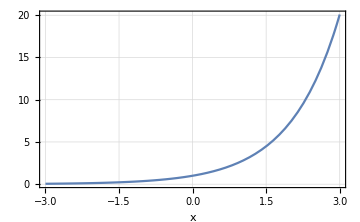

```mathematica
Plot[q2,{x,-3, 3}, PlotStyle-> tylw, GridLines->Automatic, Frame-> True, AxesOrigin-> {0, 0}, AxesLabel->Automatic, ImageSize->Medium]
```

Separable equations

```mathematica
q1 = DSolve[y'[x]==2*x*y[x]/(x+1), y[x], x]
```

{{y[x]→ⅇ^(2 (x-Log[1+x])) C[1]}}

```mathematica
q2 = Table[y[x]/.A/.{C[1]->k}, {k, 2,5}]
```

{{2 ⅇ^(2 (x-Log[1+x]))},{3 ⅇ^(2 (x-Log[1+x]))},{4 ⅇ^(2 (x-Log[1+x]))},{5 ⅇ^(2 (x-Log[1+x]))}}

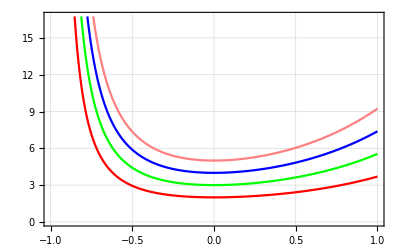

```mathematica
Plot[{q2}, {x, -1, 1}, PlotStyle->{Red, Green, Blue, Pink}, GridLines-> Automatic, Frame->True, AxesOrigin->{0,0}]
```

Initial Value Problem
This type of problem does not contain constant

```mathematica
q1 = DSolve[{y'[x] == y[x]+2/x*y[x],y[1] == 1}, y[x], x]
```

{{y[x]→ⅇ^(-1+x) x^2}}

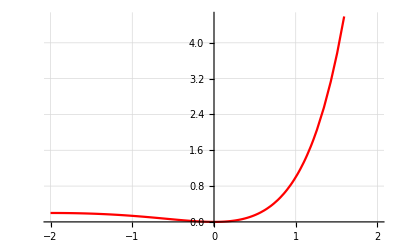

```mathematica
Plot[y[x]/.q1, {x, -2, 2}, PlotStyle-> {Red}, GridLines->Automatic]
```

Homogenous Equations

```mathematica
q1 = DSolve[y'[x] == (x+y[x])/(x), y[x], x]
```

{{y[x]→x C[1]+x Log[x]}}

```mathematica
q2 = Table[y[x]/.q1/.{C[1]-> k}, {k,2,5}]
```

{{2 x+x Log[x]},{3 x+x Log[x]},{4 x+x Log[x]},{5 x+x Log[x]}}

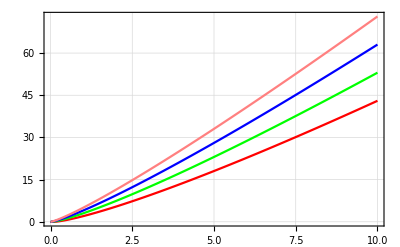

```mathematica
Plot[{q2}, {x,0,10}, PlotStyle->{Red, Green, Blue, Pink}, GridLines->Automatic, Frame->True, AxesOrigin->{0,0}]
```

Linear First Order Equations

```mathematica
q1= DSolve[y'[x]+y[x]/(x)==x^2, y[x], x]
```

{{y[x]→x^3/4+C[1]/x}}

```mathematica
q2= Table[y[x]/.sol5/.{C[1]->k}, {k, 2, 5}]
```

{{2/x+x^3/4},{3/x+x^3/4},{4/x+x^3/4},{5/x+x^3/4}}

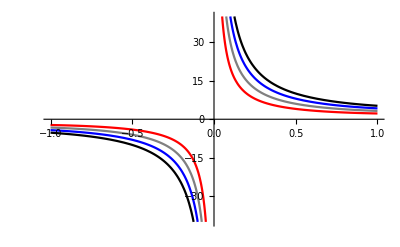

```mathematica
Plot[{q2}, {x,-1,1}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends->Automatic]
```

```mathematica
Plot[{q2}, {x,-1,1}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends->Placed[Automatic, Below]]
```

-Graphics-

```mathematica
q3 = DSolve[{y'[x]*Tan[x] == 2*y[x]-8, y[Pi/2]== 0}, y[x], x]
```

{{y[x]→4 Cos[x]^2}}

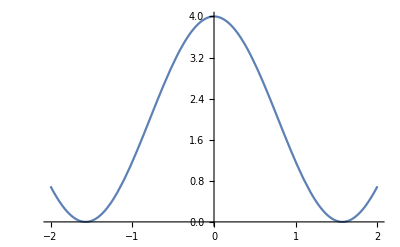

```mathematica
Plot[y[x]/.q3, {x, -2, 2}]
```

Bernoulli Equations

```mathematica
q1 = DSolve[x*y'[x]+y[x] == y[x]^2x^2+1, y[x], x]
```

{{y[x]→Tan[x+C[1]]/x}}

```mathematica
q2 = Table[y[x]/.q1/.{C[1]->k}, {k,1,4}]
```

{{Tan[1+x]/x},{Tan[2+x]/x},{Tan[3+x]/x},{Tan[4+x]/x}}

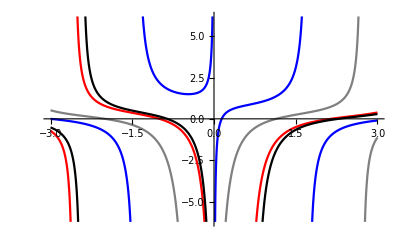

```mathematica
Plot[{q2}, {x,-3,3}, PlotStyle->{Red, Gray, Blue, Black}, PlotLegends-> Placed["Expressions", Right]]
```

Exact Equations

```mathematica
M1[x_, y_] :=(xy^2+x)
N1[x_,y_] := (yx^2)
Simplify[D[M1[x,y], y]-D[N1[x, y], x]]
```

0

```mathematica
eq1 = y'[x] == -M1[x, y[x]]/N1[x, y[x]]
```

y'[x]==(-x-x y[x]^2)/(x^2 y[x])

```mathematica
q1 = DSolve[eq1, y[x], x]
```

{{y[x]→-(√(ⅇ^(2 C[1])-x^2))/x},{y[x]→(√(ⅇ^(2 C[1])-x^2))/x}}

```mathematica
p[x_, y_]:= -(5x^2-2y^2+11)
q[x_, y_] := (Sin[y]+4xy+3)
Simplify[D[p[x,y], y]- D[q[x,y], x]]
```

4 y

Exercise

1. 3 x + 2 y dx + 2 x + y dy = 0.

```mathematica
M1[x_,y_]:=(3*x+2*y)
N1[x_,y_]:=(2*x+y)
Simplify[D[M1[x,y],y]-D[N1[x,y],x]]
```

0

```mathematica
eqn=y'[x]==-M1[x,y[x]]/N1[x,y[x]]
```

y'[x]==(-3 x-2 y[x])/(2 x+y[x])